We first read the Raw Path Data and then reproduce all the further calculation here.

```mathematica
A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Pathdata2_1_0.05.mat"];
```

```mathematica
Dimensions[A]
```

{1,81,81,201}

```mathematica
h=0.05;
htime=0.05;

length = Floor[4/h];
time =Floor[10/htime];
xf= Array[(#-length/2 -1)*h&,{length+1}];
xi=xf
```

{-2.,-1.95,-1.9,-1.85,-1.8,-1.75,-1.7,-1.65,-1.6,-1.55,-1.5,-1.45,-1.4,-1.35,-1.3,-1.25,-1.2,-1.15,-1.1,-1.05,-1.,-0.95,-0.9,-0.85,-0.8,-0.75,-0.7,-0.65,-0.6,-0.55,-0.5,-0.45,-0.4,-0.35,-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.}

```mathematica
V[x_]:=b*x+k*x^2+l*x^4+c;
```

```mathematica
k= -1; b=0.0; l=1; c=0;
```

```mathematica
L=ConstantArray[0,{length+1, length+1,time}];
S=ConstantArray[0,{length+1, length+1,time}];
Psi=ConstantArray[0,{length+1, time}];



For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

L[[i,j,t]]= (A[[1,i,j,t]]-A[[1, i,j,t-1]])^2/(2*htime*htime)-V[A[[1,i,j,t]]]; 
]
]
]


For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

S[[i,j,t]]= htime*Sum[L[[i,j,u]],{u,t}]; 
]
]
]
```

The other factors;

```mathematica
Phi=ConstantArray[0,{length+1, length+1,time-1}];
Phi2=ConstantArray[0,{length+1, length+1,time-1}];
```

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time+1,t++,

Phi[[i,j,t-1]]= htime*Sum[Sqrt[V''[A[[1,i,j,u]]]],{u,t}]; 
]
]
]
```

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time+1,t++,

Phi2[[i,j,t-1]]= htime*Sum[1/V''[A[[1,i,j,u]]],{u,t}]; 
]
]
]
```

```mathematica
Diff[y_,n_]:=D[Sqrt[x/Sin[x]],{x,n}]/.{x->y}
```

```mathematica
Q=Sum[1/(n!)((I*l*Phi2)/4)^n*Diff[Phi,2n],{n,0,1}]
```

{1}
 |  |  |  |

Initial Conditions:

```mathematica
sigma=0.3;

aorigin=I*Sqrt[k/2];
Gauss[x_]:= 1/(Sqrt[2*Pi]*sigma)Exp[-1/2*((x-aorigin)/sigma)^2]
```

Finding the wavefunction:

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

Psi[[j,t]]= h*Sum[ 1/(Sqrt[2*Pi*I*t]*sigma)Exp[I*S[[i,j,t]]]*(1+Q[[i,j,t]])*Gauss[xi[[i]]],{i,length+1}]; 
]
]
```

```mathematica
PsiN=ConstantArray[0,{time-1}];
For[t=2,t<time,t++,

PsiN[[t]]= h*Sum[ Abs[Psi[[i,t]]^2],{i,length+1}]; 
]
```

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

Psi[[j,t]]=Psi[[j,t]]/(2*Sqrt[PsiN[[t]]]); 
]
]
```

```mathematica
Sum[Abs[Psi[[j,113]]^2],{j,length+1}]
```

1.

```mathematica
Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Psi4_1_0.25.mat", Psi];
```

```mathematica
PsiT=Transpose[Psi];
```

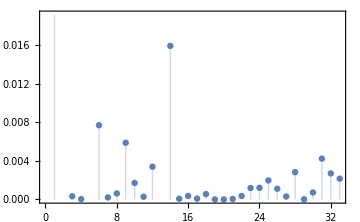

```mathematica
ListPlot[{Abs[PsiT[[180]]]^2},Frame->True,FrameStyle->Directive[GrayLevel[0],Thickness[Medium]],ImageSize->Medium,Filling->Axis, PlotStyle->Thick]
```

```mathematica
MatrixPlot[Abs[Psi]^2, ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
PsiShort=ConstantArray[0,{length+1, time/4}];
```

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time/4+1,t++,

PsiShort[[j,t]]=Psi[[j,t]]; 
]
]
```

```mathematica
ListPlot3D[Abs[Transpose[Psi]]^2, PlotRange->{0,6}]
```

-Graphics3D-

```mathematica
ListPlot3D[Abs[Transpose[PsiShort]]^2, PlotRange->Full]
```

-Graphics3D-

```mathematica
PsiR=ConstantArray[0,{length/2+1, time}];
PsiL=ConstantArray[0,{length/2+1, time}];

PR=ConstantArray[0,{time}];
PL=ConstantArray[0,{time}];

For[j=1,j<length/2+2,j++,
For[t=2,t<time,t++,

PsiL[[j,t]]=Psi[[j,t]]; 
]
]


For[j=length/2+1,j<length+2,j++,
For[t=2,t<time,t++,

PsiR[[j-(length/2),t]]=Psi[[j,t]]; 
]
]




For[t=2,t<time,t++,

PL[[t]]=Sum[Abs[PsiL[[j,t]]^2],{j,1,length/2}]; 
]

For[t=2,t<time,t++,

PR[[t]]=Sum[Abs[PsiR[[j,t]]^2],{j,1,length/2+1}]; 
]
```

```mathematica
MatrixPlot[Abs[PsiL]^2, ImageSize->Full, PlotTheme->"Detailed"]
MatrixPlot[Abs[PsiR]^2, ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

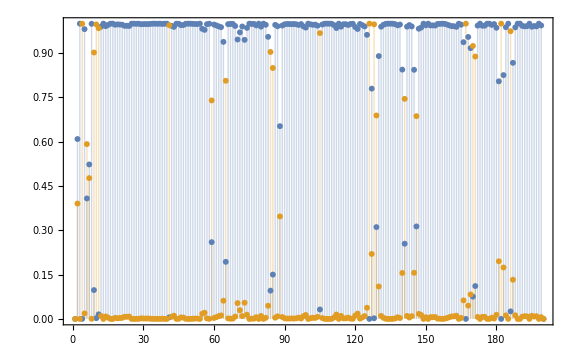

```mathematica
ListPlot[{PL,PR},Frame->True,FrameStyle->Directive[GrayLevel[0],Thickness[Medium]],ImageSize->Large,Filling->Axis, PlotStyle->Thick]
```

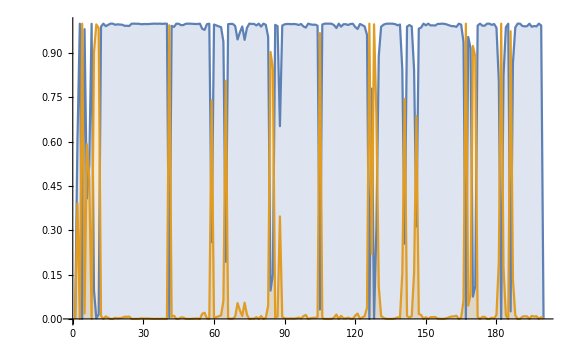

```mathematica
ListPlot[{PL,PR},MaxPlotPoints->Infinity,Joined->True, Filling->Axis,ImageSize->Large]
```